Auswertung für Praktikum: Luminescence Spectroscopy
In diesem Notebook findet die Auswertung der Daten statt. Zunächst werden eine hilfreiche Funktionen definiert um Redundanzen zu vermeiden und dann wird jeder Datensatz mit individuellen Parametern gefittet.

{100K.dat,110K.dat,120K.dat,130K.dat,140K.dat,150K.dat,165K.dat,180K.dat,195K.dat,210K.dat,225K.dat,240K.dat,255K.dat,80K_10ms.dat,80K_1ms.dat,80K_50ms.dat,90K.dat,ohneLed.dat}

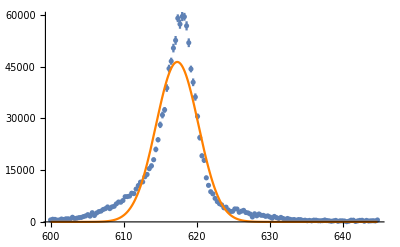

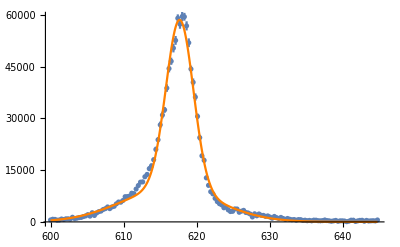

```mathematica
(* Lade ErrorBar Package *)
Needs["ErrorBarPlots`"];

(* Setze Directory wo Messdaten liegen*)
SetDirectory["/Users/chegerland/Desktop/Praktikum_LUM/Messung/"];

(* ----------------------------------------------------------------------- *)
(* ----------------------------- Funktionen ------------------------------ *)
(* ----------------------------------------------------------------------- *)

(* importdata: Schneide Datenpunkte mit Fehler = 0 raus (Probleme bei Fit) *)
importdata[data_]:=DeleteCases[
Select[#,UnequalTo[0]]&/@Transpose[{data[[All,2]],data[[All,3]],data[[All,4]]}],
x_/;Length[x]≠3];

(* Fitmodelle model(Gauß) und model2(Doppelgauß) *)
model[ampl_,x0_,sigm_,x_]:=ampl*1/Sqrt[2*Pi*sigm^2]*Exp[-(x-x0)^2/(2 sigm^2)];
model2[ampl_,x0_,sigm_,ampl2_,x02_,sigm2_,x_]:=ampl*1/Sqrt[2*Pi*sigm^2]*Exp[-(x-x0)^2/(2 sigm^2)]+ampl2*1/Sqrt[2*Pi*sigm2^2]*Exp[-(x-x02)^2/(2 sigm2^2)];

(* f: Erstelle Fits (Gauß und Doppelgauß) mit geschätzten Peakpositionen/Amplituden *)
f[data_,x0guess_,amplguess_,x02guess_]:={
NonlinearModelFit[Transpose[{data[[All,1]],data[[All,2]]}],model[ampl,x0,sigm,x],{sigm,{x0,x0guess},{ampl,amplguess}},x,Weights->1/data[[All,3]]^2],
NonlinearModelFit[Transpose[{data[[All,1]],data[[All,2]]}],model2[ampl,x0,sigm,ampl2,x02,sigm2,x],{sigm,{x0,x0guess},{ampl,amplguess},ampl2,{x02,x02guess},sigm2},x,Weights->1/data[[All,3]]^2]
};

(* g: Zeige Fits + Datenpunkte mit Fehlerbalken *)
g[data_,list_,index_]:=Show[
ErrorListPlot[data,PlotRange->Full],Plot[list[[index]][y],{y,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Orange,PlotRange->Full]
];

(* ----------------------------------------------------------------------- *)
(* ----------------------------- Rechnungen ------------------------------ *)
(* ----------------------------------------------------------------------- *)

(* Importiere Daten in große Liste *)
data = {};
Importfiles = FileNames["*.dat"];
For[i=1,i≤Length[Importfiles],i++,AppendTo[data,importdata[Import[Importfiles[[i]]]]]];

(* initiiere Fitliste und hänge folgende Datensätze an *)
fits = {};
i=0;

(* 100K *)
i++;
AppendTo[fits,f[data[[i]],615,70000,610]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];

(* 110K *)
i++;
AppendTo[fits,f[data[[i]],615,67000,628]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];

(* 120K *)
i++;
AppendTo[fits,f[data[[i]],615,60000,628]];
g[data[[i]],fits[[i]],1];
g[data[[i]],fits[[i]],2];
fits[[i,1]]["ParameterTable"];
fits[[i,2]]["ParameterTable"];
```